# ODVOD Kaj je odvod? Odvod v matematiki predstavlja spremembo funkcije pri spremembi njenega argumenta. Opisuje najboljši linearno aproksimacijo funkcije v bližni vrednosti funkcije z nekim argumentom. -Graphics-

# ODVOD FUNKCIJE

## odvod funkcije - v določeni točki je limita deferenčnega kvocienta Δy/Δx, ko gre Δx proti nič. geometrijski pomen odvod- vrednost odvoda funkcije v x0 je enaka smernemu koeficientu tangente na graf funkcije v točki z absciso x0 kot pod katerim seka krivulja os x - je enak naklonskemu kotu tangente na krivuljo v presečišču z osjo x. kot pod katerim krivulja seka os x - je enak kotu med tangentama na obe krivulji v njunem presečišču

PRAVILA ZA ODVAJANJE: 
Odvod konstante funkcije                                                  (c ’) = 0 
Odvod potenčne funkcije                                                              (x^n)' = n* x^(n - 1)
Odvod vsote funkcij                                                              ( f + g)’ = f ’ + g ’
Odvod zmnožka dveh funkcij                                          (f ’ × g’) = f ’ × g + f × g ’
Odvod zmnožka funkcije s konstantno funkcijo    (c × f)’ = c × f ’
Odvod količnika dveh funkcij                                          (f/g)' = (f ' * g - f* g')/g^2

1. NALOGA - določi enačbo tangente na graf x^2+ y^2= 1, x =1/2

```mathematica
Solve[(1/2)^2+y^2 ==1]
```

{{y→-(√3)/2},{y→(√3)/2}}

```mathematica
Solve[D[x^2+y[x]^2==1,x],y'[x]]/.{x->1/2,y[x]->(√3)/2}
```

{{y'[1/2]→-1/(√3)}}

```mathematica
Solve[(√3)/2==-1/3*(1/2)+ b,b]
```

{{b→1/6 (1+3 √3)}}

WolframAlphaQueryParseResults

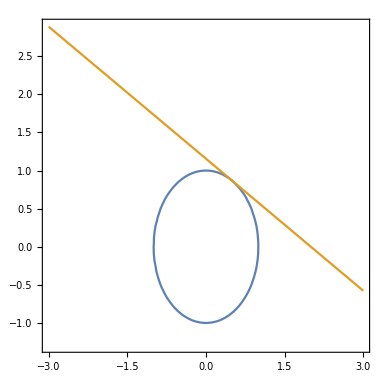

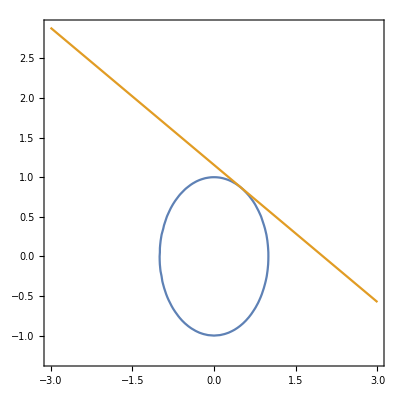

```mathematica
Show[%1,Axes->True,AxesStyle->Gray]
```

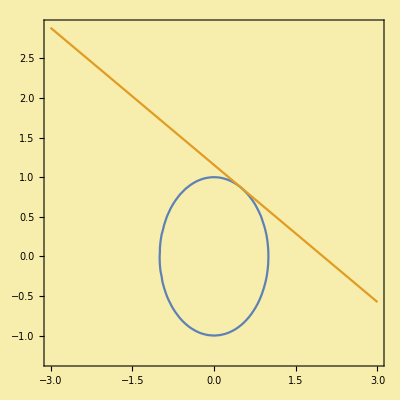

```mathematica
Show[%2,Background->RGBColor[0.97,0.93,0.68]]
```

2. NALOGA - odvajaj f(x) = sinx in nariši graf, 3D in multiplication.

```mathematica
D[Sin[x],x]
```

Cos[x]

WolframAlphaQueryParseResults

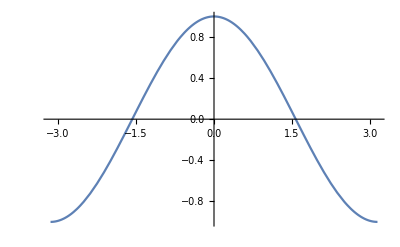

```mathematica
Manipulate[Plot[Cos[frequency*x],{x,0,2π}],{frequency,1,5}]
```

WolframAlphaQueryParseResults

-Graphics3D-

```mathematica
Show[%4,Background->RGBColor[0.44,1.,0.68]]
```

-Graphics3D-

3.NALOGA - pokaži, da y = 6 x^3+5x +6 nima naklona pri 4

```mathematica
f = 6 x^3+5x -3
D[f,x]
```

-3+5 x+6 x^3

5+18 x^2

```mathematica
Solve[18 x^2+5==4,x]
```

{{x→-ⅈ/(3 √2)},{x→ⅈ/(3 √2)}}

5+18 x^2

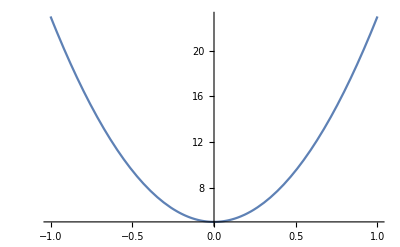

```mathematica
g = 18 x^2+5
Plot[g,{x,-1,1}]
```

4. NALOGA Določite funkcijo z eno spremenljivko, f(x) l = x^3- sin( x^2)

```mathematica
f[x_] = x^3 - Sin[x^2]
```

x^3-Sin[x^2]

```mathematica
f'[x]
```

3 x^2-2 x Cos[x^2]

```mathematica
f'''[x]
```

6+8 x^3 Cos[x^2]+12 x Sin[x^2]

```mathematica
D[f[x],{x,3}]
```

6+8 x^3 Cos[x^2]+12 x Sin[x^2]

5.NALOGA določite funkcijo z dvema spremenljivkama: g(x, y) = (x + y)^4:

```mathematica
g[x_,y_] = (x + y)^4
```

```mathematica
(x+y)^4
D[g[x,y],x,{y,2}]
```

(x+y)^4

```mathematica
24 (x+y)
{HeavisideTheta[-1], HeavisideTheta[0],HeavisideTheta[1]}
```

{0,HeavisideTheta[0],1}

```mathematica
HeavisideTheta'[x]
```

DiracDelta[x]

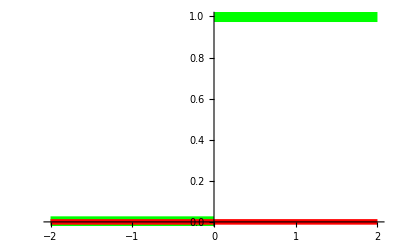

```mathematica
Plot[{HeavisideTheta[x], DiracDelta[x]},{x, -2,2},
PlotStyle->{{Thickness[.02],Green},{Thickness[.01],Red}}]
```